```mathematica
dir=NotebookDirectory[];
files=FileNames["Angles90deg_*.csv",dir];
```

```mathematica
process[file_]:=Module[{data,headers,tcol,acol,time,angle},data=Import[file,"CSV"];
headers=First[data];
tcol=First@FirstPosition[headers,"Time"];
acol=First@FirstPosition[headers,"Angle"];
time=data[[All,tcol]];
angle=data[[All,acol]];
Transpose@{Rest[time],(Rest[angle]-angle[[2]])*Pi/180}];
```

```mathematica
results = AssociationMap[process, files];
```

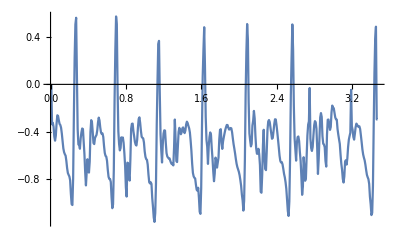
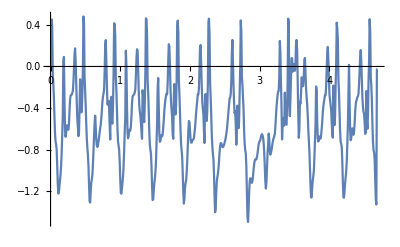
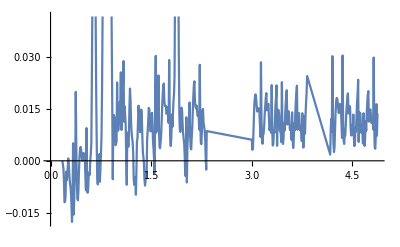
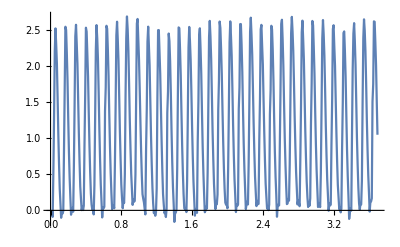
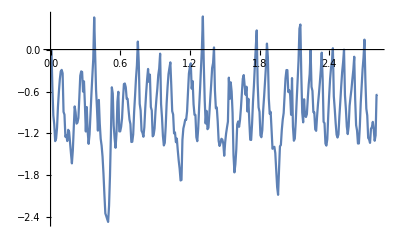
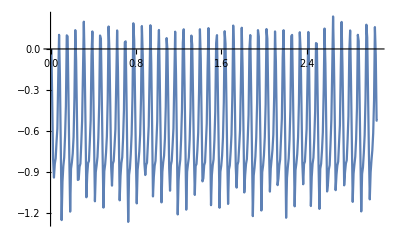

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_90deg\\Angles90deg_4cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}](*3 is postprocessed, there were spurious jumps. 4 is postprocessed, was registered as a perfect spinning mode and we substracted the linear growth.*)
```

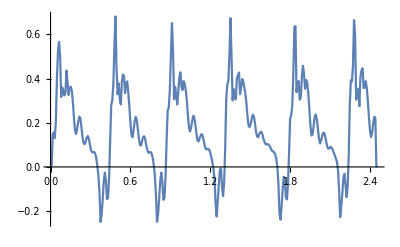
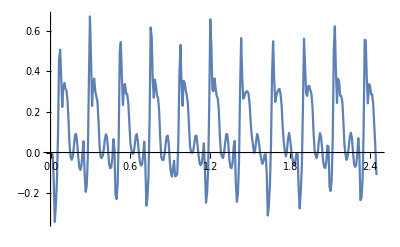
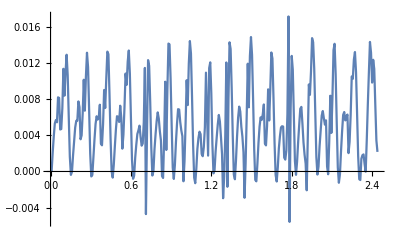
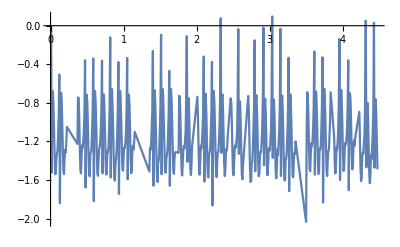
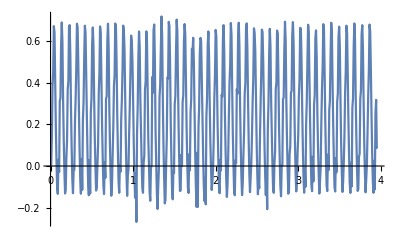
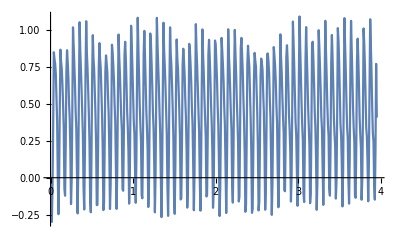

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_90deg\\Angles90deg_5cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}](*3 and 4 are postprocessed, there were spurious jumps*)
```

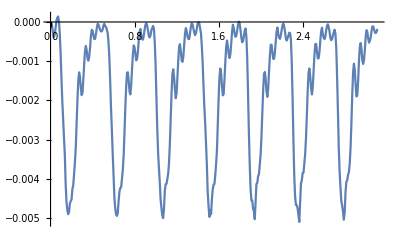
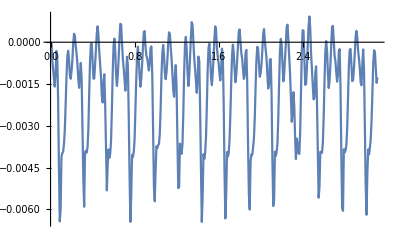
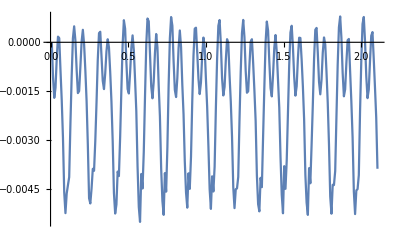
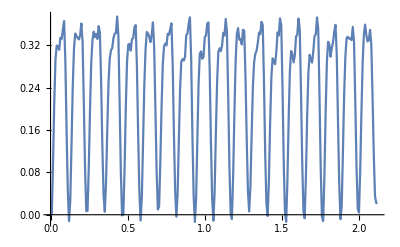
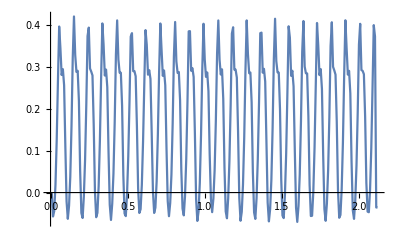
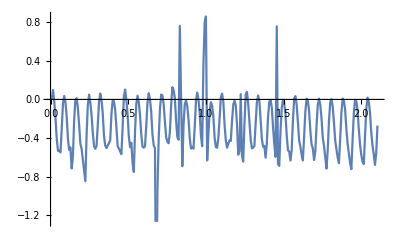

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_90deg\\Angles90deg_6cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}](*6 is postprocessed, there were spurious jumps*)
```

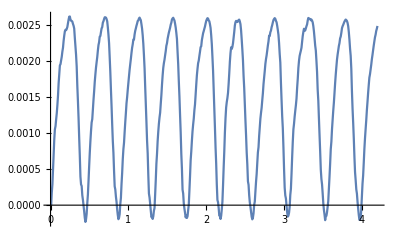
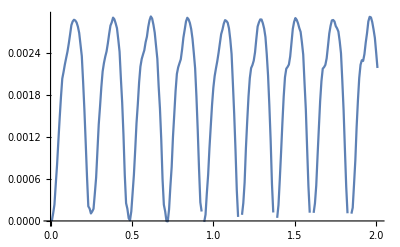
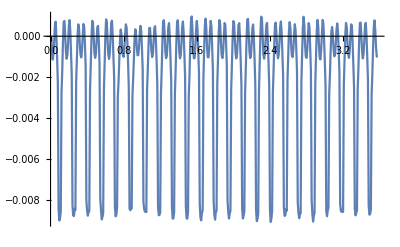
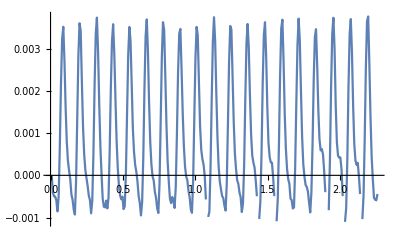
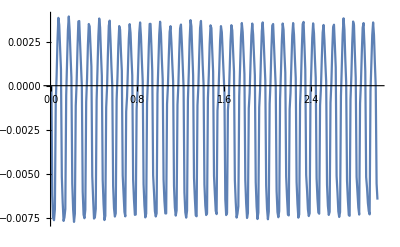
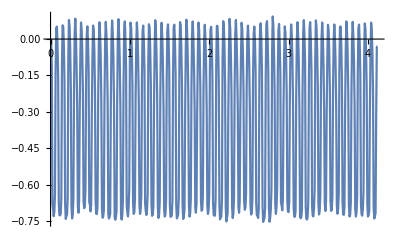

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_90deg\\Angles90deg_7cm_" <> ToString[i]<>"hz.csv"]],{i, 1, 6}]
```

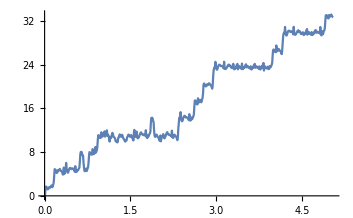
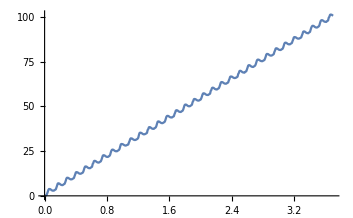

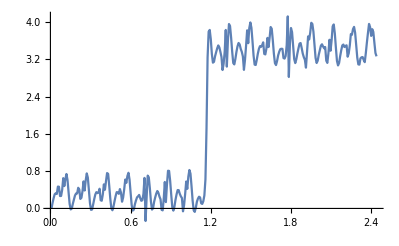
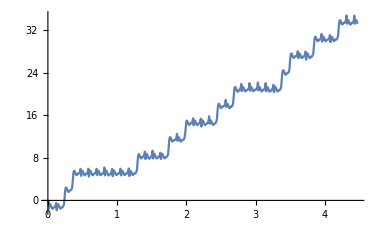

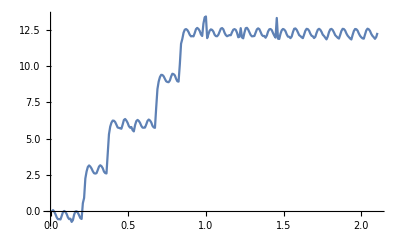

```mathematica
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_90deg\\Angles90deg_"<>ToString[i] <> "cm_6hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_90deg\\Angles90deg_"<>ToString[i] <> "cm_5hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_90deg\\Angles90deg_"<>ToString[i] <> "cm_4hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_90deg\\Angles90deg_"<>ToString[i] <> "cm_3hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_90deg\\Angles90deg_"<>ToString[i] <> "cm_2hz.csv"]], {i, 4,7}]
Table[ListLinePlot[results["C:\\Users\\mogue\\OneDrive\\Escritorio\\Pringle data\\Excel_Angles_90deg\\Angles90deg_"<>ToString[i] <> "cm_1hz.csv"]], {i, 4,7}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}